## Official lattice

S-band longitudinal wakes from official MAD8 lattice: https://www.slac.stanford.edu/cgi-bin/cvsweb/optics/etc/lattice/facet2/sband_l.dat?cvsroot=LCLS

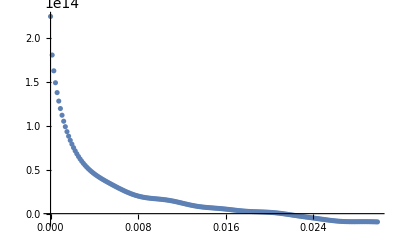

```mathematica
raw = Import["~/Downloads/sband_l.dat"];
raw=raw[[2;;]];

ListPlot[raw[[All,{2,3}]],PlotRange->All]
```

-Graphics-

## Bmad

(base) nmajik@dhcp-visitor-216-95 wakefields % cat longitudinal_wakes_sband.bmad 
! Adapted from file: 	elegant/Sz_p5um_10mm_per35mm_cell.sdds
! Usage: 
! ele[sr_wake] = call::longitudinal_wakes_sband.bmad

{
  scale_with_length = T, 
  longitudinal = {1.0214527206425931e14, 200.737972823806, 0, 0.25, none},
  longitudinal = {2.0264683145205535e13, 164752.58575866005, 0, 0.25, none},
  longitudinal = {9.111515497722739e13, 1206.8246815698092, 0, 0.25, none},
  longitudinal = {4.95817609185586e13, 9050.772842025624, 0, 0.25, none},
z_max = 0.01}

```mathematica
wakeSpecs = {
{1.02*^14, 200.737972823806},
{2.02*^13,164752.58575866005},
{9.11*^13,1206.8246815698092},
{4.96*^13,9050.772842025624}
};
```

-Graphics-

So it appears that the data file has no frequency terms! Is it just building up the wake from exponentials?

```mathematica
wakeExprs = #[[1]]*Exp[-#[[2]]*z]&/@wakeSpecs;
```

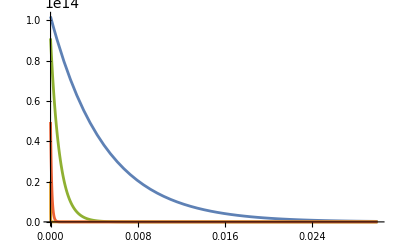

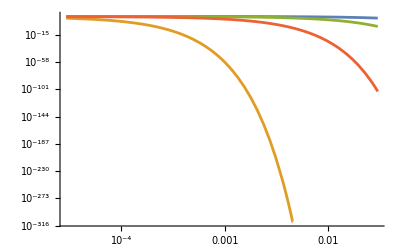

```mathematica
Plot[
wakeExprs,{z,0,0.03},
PlotRange->All
]
LogLogPlot[
wakeExprs,{z,0,0.03},
PlotRange->All
]
```

```mathematica
wakeSumExpr = Total[wakeExprs];
```

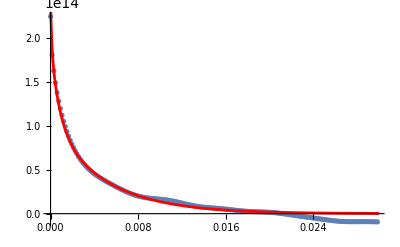

```mathematica
Show[
ListPlot[raw[[All,{2,3}]],PlotRange->All],
Plot[
wakeSumExpr,{z,0,0.03},
PlotRange->All,
PlotStyle->Red
]
]
```

Not bad! And the Bmad file specifies z_max = 0.01 and the agreement really is quite good up to that point

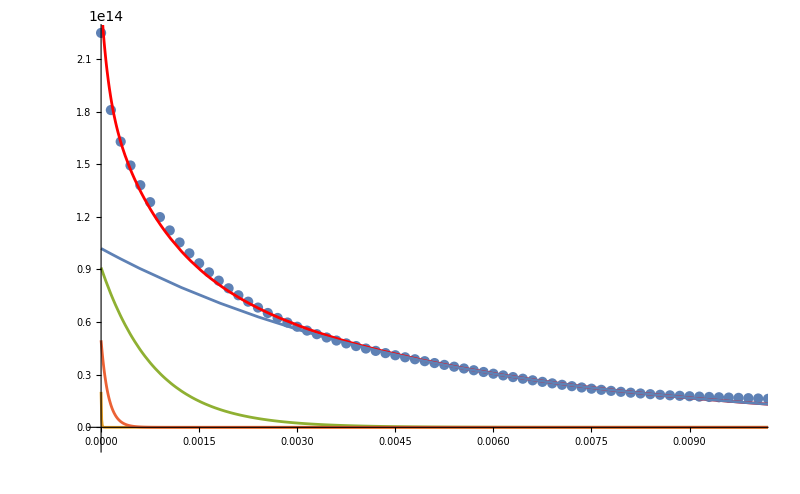

```mathematica
Show[
ListPlot[raw[[All,{2,3}]],PlotRange->{{0,0.01},All},ImageSize->800],
Plot[
wakeSumExpr ,{z,0,0.03},
PlotRange->All,
PlotStyle->Red
],
Plot[
wakeExprs,{z,0,0.03},
PlotRange->All
]
]
```

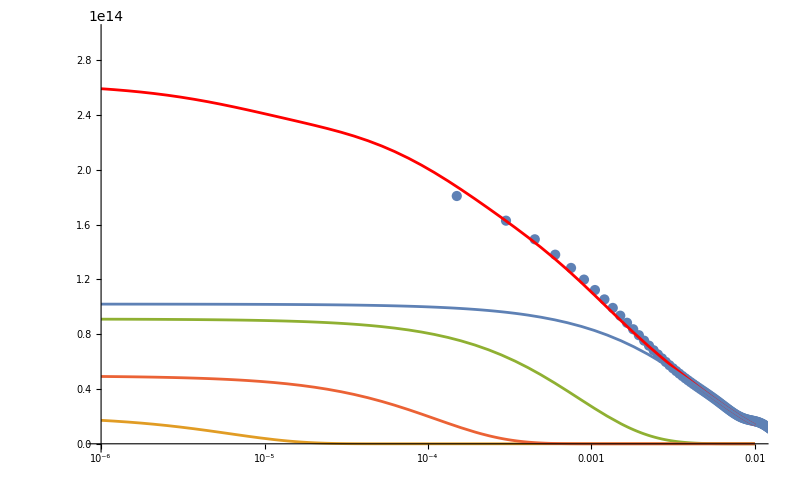

```mathematica
Show[
ListLogLinearPlot[raw[[All,{2,3}]],PlotRange->{{1*^-6,0.01},{0,3*^14}},ImageSize->800],
LogLinearPlot[
wakeSumExpr ,{z,1*^-6,0.01},
PlotRange->All,
PlotStyle->Red
],
LogLinearPlot[
wakeExprs,{z,1*^-6,0.01},
PlotRange->All
]
]
```

# Self-smart the pseudomodes

```mathematica
raw = Import["~/Downloads/sband_l.dat"];
raw=raw[[2;;]];
```

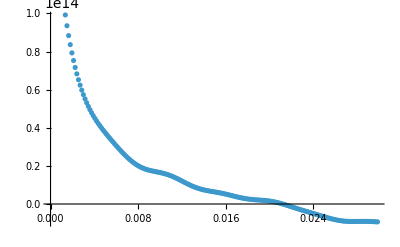

```mathematica
ListPlot[raw[[All,{2,3}]]]
```

```mathematica
fitData = Select[raw[[All,{2,3}]] ,#[[1]]<0.01&];
```

```mathematica
n=4;
expr = Sum[Subscript[a, i] * Exp[- Subscript[b, i] z],{i,1,n}]
coeffs = Flatten[
Table[{
{Subscript[a, i],i*10^13},
{Subscript[b, i],i*100}
},{i,1,n}],1]

nlm=NonlinearModelFit[
fitData,
expr,
coeffs,
z,
Method->{"NMinimize",Method->"DifferentialEvolution"},
MaxIterations->1000
]
```

ⅇ^(-z b_1) a_1+ⅇ^(-z b_2) a_2+ⅇ^(-z b_3) a_3+ⅇ^(-z b_4) a_4

{{a_1,10000000000000},{b_1,100},{a_2,20000000000000},{b_2,200},{a_3,30000000000000},{b_3,300},{a_4,40000000000000},{b_4,400}}

FittedModel[…]

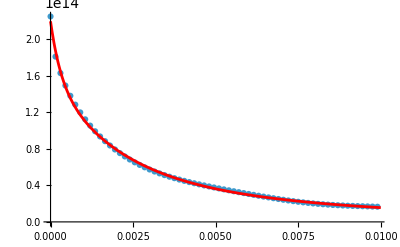

```mathematica
Show[
ListPlot[fitData],
Plot[nlm["BestFit"],{z,0,0.01},PlotStyle->{Red}]
]
```

```mathematica
nlm["BestFit"]
```

6.04711×10^13 ⅇ^(-3232.88 z)+9.48788×10^13 ⅇ^(-545.898 z)+5.32743×10^13 ⅇ^(-180.224 z)+1.09719×10^13 ⅇ^(-53.8656 z)

```mathematica
NotebookDirectory[]
```

/Users/nmajik/Documents/SLAC/git/SLAC-Containers/notebooks/BluePill/ARCHIVE/

# Transverse

# Self-smart the pseudomodes

```mathematica
raw = Import["~/Downloads/sband_t.dat"];
raw=raw[[2;;]];
```

```mathematica
ListPlot[raw[[All,{2,3}]]]
```

-Graphics-

```mathematica
(*fitData = Select[raw[[All,{2,3}]] ,#[[1]]<0.01&];*)
fitData = raw[[All,{2,3}]];
```

```mathematica
n=8;
expr = Sum[Subscript[a, i] * Exp[- Subscript[b, i] z],{i,1,n}]
coeffs = Flatten[
Table[{
{Subscript[a, i],RandomReal[{-1*^16,1*^16}]},
{Subscript[b, i],RandomReal[{0,2000}]}
},{i,1,n}],1]

nlm=NonlinearModelFit[
fitData,
expr,
coeffs,
z,
Method->{"NMinimize",(*Method->"NelderMead"*)Method->"DifferentialEvolution"},
MaxIterations->5000
]
```

ⅇ^(-z b_1) a_1+ⅇ^(-z b_2) a_2+ⅇ^(-z b_3) a_3+ⅇ^(-z b_4) a_4+ⅇ^(-z b_5) a_5+ⅇ^(-z b_6) a_6+ⅇ^(-z b_7) a_7+ⅇ^(-z b_8) a_8

{{a_1,-6.57006×10^15},{b_1,708.182},{a_2,-7.11247×10^14},{b_2,1879.92},{a_3,-5.56512×10^15},{b_3,1414.85},{a_4,-9.84661×10^15},{b_4,990.082},{a_5,8.87719×10^15},{b_5,449.374},{a_6,-5.31842×10^15},{b_6,899.578},{a_7,-1.10676×10^15},{b_7,1477.3},{a_8,9.78755×10^14},{b_8,401.758}}

FittedModel[…]

```mathematica
Show[
ListPlot[fitData],
Plot[nlm["BestFit"],{z,0,0.03},PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
nlm["BestFit"]
```

2.28859×10^14 ⅇ^(-3.06193×10^6 z)+1.00903×10^14 ⅇ^(-153138. z)-1.05973×10^15 ⅇ^(-1926.07 z)+0.877099 ⅇ^(-1628.24 z)+4.82562×10^15 ⅇ^(-341.268 z)-1.23792×10^16 ⅇ^(-257.796 z)+9.04626×10^15 ⅇ^(-45.4564 z)-4.66534×10^14 ⅇ^(61.421 z)

```mathematica
Show[
ListPlot[raw[[All,{2,3}]]],
Plot[-4.844529962492917*^15 ⅇ^(-482.3623602777055 z)+1.2118183974655531*^13 ⅇ^(-482.36106239708 z)+6.66223178971757*^14 ⅇ^(-151.377072161524 z)+4.22896560940384*^15 ⅇ^(-4.941341025532096 z),{z,0,0.03},PlotStyle->{Red},PlotRange->All]
]
```

-Graphics-